```mathematica
V =(m^2 ϕ^2)/2+(-1/3-a^2 m^2) ϕ^3+(a^2+(23 a^4 m^2)/6+(112 a^6 m^4)/9+(400 a^8 m^6)/9+(5056 a^10 m^8)/45+(30848 a^12 m^10)/135+(372224 a^14 m^12)/945+(111872 a^16 m^14)/189+(959488 a^18 m^16)/1215+(40306688 a^20 m^18)/42525+(483713024 a^22 m^20)/467775) ϕ^4+(-(13 a^4)/3-(370 a^6 m^2)/9-(2356 a^8 m^4)/9) ϕ^5+((97 a^6)/3+(7444 a^8 m^2)/15+(40016 a^10 m^4)/27+(16951588 a^12 m^6)/2025+(365040328 a^14 m^8)/4725+(704360354 a^16 m^10)/1575+(53044107164 a^18 m^12)/25515+(5345363837636 a^20 m^14)/637875+(212689374482008 a^22 m^16)/7016625) ϕ^6+(-(13532 a^8)/45-(1645424 a^10 m^2)/405-(246594764 a^12 m^4)/6075-(18403444376 a^14 m^6)/42525) ϕ^7+((1057238 a^10)/405+(528895198 a^12 m^2)/8505+(293278365536 a^14 m^4)/297675+(330220197478 a^16 m^6)/297675+(4539699316064 a^18 m^8)/535815+(3762791962092662 a^20 m^10)/13395375+(18508000088422676 a^22 m^12)/5893965) ϕ^8+(-(17612426 a^12)/567-(1376189404 a^14 m^2)/1323-(1461162201244 a^16 m^4)/178605-(152243548796524 a^18 m^6)/1607445-(14516307774038468 a^20 m^8)/8037225) ϕ^9+((17745598574 a^14)/42525+(91967935202338 a^16 m^2)/8037225+(3255947000654108 a^18 m^4)/14467005+(339406560100146388 a^20 m^6)/72335025-(36650456262120146896 a^22 m^8)/3978426375) ϕ^10+(-(5599006958392 a^16)/1148175-(2226671149812904 a^18 m^2)/10333575-(461350316377218328 a^20 m^4)/72335025-(13262953310597307088 a^22 m^6)/795685275) ϕ^11+((604370472837748 a^18)/8037225+(3570960644823919238 a^20 m^2)/795685275+(107753866659559323248 a^22 m^4)/1705039875) ϕ^12+(-(1954323884798776 a^20)/1515591-(60074374172932678156 a^22 m^2)/1023023925) ϕ^13+(11898606015180066008 a^22 ϕ^14)/651015225/.{a-> ξ,m-> I};
```

```mathematica
Plotter[order_]:=Module[{list,length,ratio,log,range},

list=CoefficientList[SeriesCoefficient[V,{ϕ,0,order}],ξ^2];
length=Length[list];
ratio=Table[{2i-2,Abs[list[[i+1]]/list[[i]]]},{i,order-2,length-1}];
log = Table[{2i-2,Log[Abs[list[[i]]]]},{i,order-2,length}];
range =Plot[{n,1},{n,0,22},PlotRange->All];
Show[range,ListPlot[{log, ratio}]]
];
```

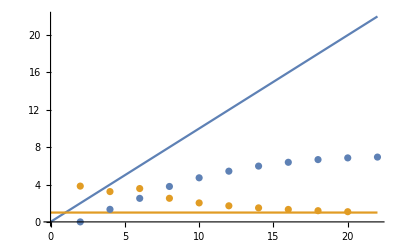

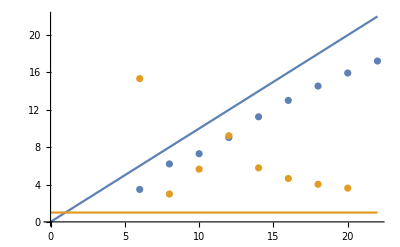

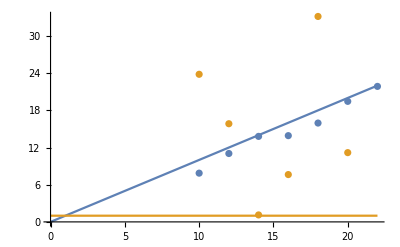

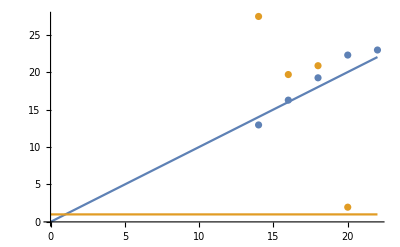

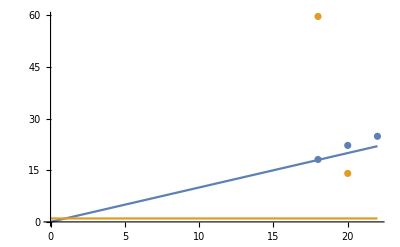

```mathematica
Plotter[4]
Plotter[6]
Plotter[8]
Plotter[10]
Plotter[12]
```

Table::iterb: Iterator {i,-2+order,0} does not have appropriate bounds.

Table::iterb: Iterator {i,-2+order,1} does not have appropriate bounds.

Table::iterb: Iterator {i,-2.+order,1.} does not have appropriate bounds.

Table::iterb: Iterator {i,-2.+order,0} does not have appropriate bounds.

Table::iterb: Iterator {i,-2.+order,1.} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

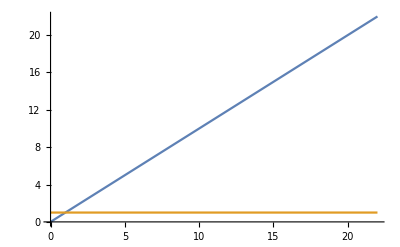

```mathematica
list=CoefficientList[SeriesCoefficient[V,{ϕ,0,order}],ξ^2];
length=Length[list];
ratio=Table[{2i-2,Abs[list[[i+1]]/list[[i]]]},{i,order-2,length-1}];
log = Table[{2i-2,Log[Abs[list[[i]]]]},{i,order-2,length}];
range =Plot[{n,1},{n,0,22},PlotRange->All];
Show[range,ListPlot[{log, ratio}]]
```